```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory["~/Desktop/Work/analysis"]
```

/users/home/arway/Desktop/Work/analysis

```mathematica
a[θ_,ϕ_]:=Sin[θ]Cos[ϕ];
b[θ_,ϕ_]:=Sin[θ]Sin[ϕ];
c[θ_,ϕ_]:=Cos[θ];
d[θ_,ϕ_]:=(2 a[θ,ϕ]^2-1)/(2 c[θ,ϕ]);
e[θ_,ϕ_]:=√(1-a[θ,ϕ]^2-d[θ,ϕ]^2)
```

```mathematica
sA[θ_,ϕ_]:={a[θ,ϕ],b[θ,ϕ],c[θ,ϕ]}
sB[θ_,ϕ_]:={d[θ,ϕ],e[θ,ϕ],-a[θ,ϕ]};
sC[θ_,ϕ_]:={-e[θ,ϕ],-c[θ,ϕ]-d[θ,ϕ],-b[θ,ϕ]};
sD[θ_,ϕ_]:={-a[θ,ϕ],-b[θ,ϕ],-c[θ,ϕ]};
sE[θ_,ϕ_]:={-d[θ,ϕ],-e[θ,ϕ],a[θ,ϕ]};
sF[θ_,ϕ_]:={e[θ,ϕ],c[θ,ϕ]+d[θ,ϕ],b[θ,ϕ]};
```

```mathematica
sA[1,1]//N
```

{0.454649,0.708073,0.540302}

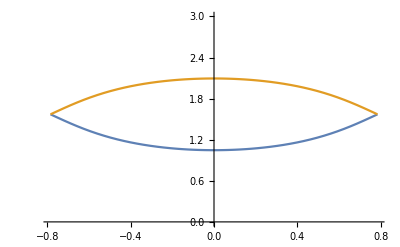

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[Sqrt[(4-Sqrt[16-6 (1-Cos[4 ϕ])])/(1-Cos[4 ϕ])]]]
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π/4,π/4},PlotRange->{{-π/4,π/4},{0,3}}]
```

```mathematica
animate=Manipulate[Show[{Graphics3D[{Black,Arrowheads[0.1],Arrow[Tube[{{-1,-1,-1},{1,1,1}},0.01]]}],Graphics3D[{Red,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sA[θ,ϕ]},0.01]]}],Graphics3D[{Green,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sB[θ,ϕ]},0.01]]}],Graphics3D[{Blue,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sC[θ,ϕ]},0.01]]}],Graphics3D[{Pink,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sD[θ,ϕ]},0.01]]}],Graphics3D[{Brown,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sE[θ,ϕ]},0.01]]}],Graphics3D[{Purple,Arrowheads[0.1],Arrow[Tube[{{0,0,0},sF[θ,ϕ]},0.01]]}]},AspectRatio->1,ViewPoint->{70,10,15},ImageSize->{300,200}]
Show[boundPlot,ListPlot[{{ϕ,θ}}],ImageSize->{340,200}],{θ,0,π,.01},{ϕ,-π/4,π/4,0.01},ContentSize->{700,250}]
```

```mathematica
Export["GroundStateView.avi",animate,"Framerate"->60]
```

GroundStateView.avi